1

0

0

{(0.5-0.5 ⅈ) ⅇ^((0.0000124998-0.100166 ⅈ) n)+(0.5+0.5 ⅈ) ⅇ^((0.0000124998+0.100166 ⅈ) n),(0.5+0.5 ⅈ) ⅇ^((0.0000124998-0.100166 ⅈ) n)+(0.5-0.5 ⅈ) ⅇ^((0.0000124998+0.100166 ⅈ) n)}

(0.5-0.5 ⅈ) ⅇ^((0.0000124998-0.100166 ⅈ) n)+(0.5+0.5 ⅈ) ⅇ^((0.0000124998+0.100166 ⅈ) n)

(0.5+0.5 ⅈ) ⅇ^((0.0000124998-0.100166 ⅈ) n)+(0.5-0.5 ⅈ) ⅇ^((0.0000124998+0.100166 ⅈ) n)

0.005

-0.005

{ⅇ^((0.-0.100042 ⅈ) n) ((0.5-0.475595 ⅈ)+(0.5+0.475595 ⅈ) ⅇ^((0.+0.200083 ⅈ) n)),ⅇ^((0.-0.100042 ⅈ) n) ((0.5+0.475595 ⅈ)+(0.5-0.475595 ⅈ) ⅇ^((0.+0.200083 ⅈ) n))}

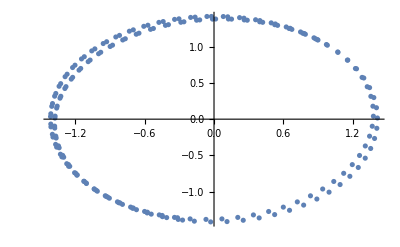

```mathematica
sys:={Subscript[x, 1][n + 1]- (0.995+a) Subscript[x, 1][n] + 0.1 Subscript[x, 2][n] == 0, Subscript[x, 2][n + 1]- 0.1 Subscript[x, 1][n] - (0.995+b) Subscript[x, 2][n] == 0,Subscript[x, 1][0]==Subscript[x, 10],Subscript[x, 2][0]==Subscript[x, 20]}

Subscript[x, 10]=1;Subscript[x, 20]=1

a=0
b=0
sol1=RSolveValue[sys, {Subscript[x, 1][n],Subscript[x, 2][n]}, {n}]//Simplify
m1[n_]=sol1[[1]]
m2[n_]=sol1[[2]]

x1sol1[n_]:=(0.5-0.5 ⅈ) ⅇ^((0.000012499843752955542-0.10016616488792511 ⅈ) n)+(0.5+0.5 ⅈ) ⅇ^((0.000012499843752955542+0.10016616488792511 ⅈ) n)
x2sol1[n_]:=(0.5+0.5 ⅈ) ⅇ^((0.000012499843752955542-0.10016616488792511 ⅈ) n)+(0.5-0.5 ⅈ) ⅇ^((0.000012499843752955542+0.10016616488792511 ⅈ) n)

plot1:=ListPlot[Table[{x1sol1[i], x2sol1[i]}, {i, 100}]]


a=0.005
b=-0.005
sol2=RSolveValue[sys, {Subscript[x, 1][n],Subscript[x, 2][n]}, {n}]//Simplify

x1sol2[n_]:=ⅇ^((0.-0.10004171361154002 ⅈ) n) ((0.5-0.475594865605671 ⅈ)+(0.5+0.475594865605671 ⅈ) ⅇ^((0.+0.20008342722308003 ⅈ) n))
x2sol2[n_]:=ⅇ^((0.-0.10004171361154002 ⅈ) n) ((0.5+0.475594865605671 ⅈ)+(0.5-0.475594865605671 ⅈ) ⅇ^((0.+0.20008342722308003 ⅈ) n))

plot2:=ListPlot[Table[{x1sol2[i], x2sol2[i]}, {i, 100}]]

Show[plot1,plot2]
```